## Modi Cupola

## Determinazione dell’equazione caratteristica

```mathematica
ψ[x_]=α Cos[β x]c1+α Sin[β x]c2+γ ⅇ^(δ x)c3+γ ⅇ^(-δ x)c4+c5+x c6;
```

```mathematica
cc1=ψ[0]==0;
```

```mathematica
Collect[cc1,{c1,c2,c3,c4,c5,c6}]
```

c5+c1 α+c3 γ+c4 γ==0

```mathematica
cc2=ψ'[0]==0;
```

```mathematica
Collect[cc2,{c1,c2,c3,c4,c5,c6}]
```

c6+c2 α β+c3 γ δ-c4 γ δ==0

```mathematica
cc3=ψ''[0]==0;
```

```mathematica
Collect[cc3,{c1,c2,c3,c4,c5,c6}]
```

-c1 α β^2+c3 γ δ^2+c4 γ δ^2==0

```mathematica
cc4=ψ[l]==0;
```

```mathematica
Collect[cc4,{c1,c2,c3,c4,c5,c6}]
```

c5+c6 l+c4 ⅇ^(-l δ) γ+c3 ⅇ^(l δ) γ+c1 α Cos[l β]+c2 α Sin[l β]==0

```mathematica
cc5=ψ'[l]==0;
```

```mathematica
Collect[cc5,{c1,c2,c3,c4,c5,c6}]
```

c6-c4 ⅇ^(-l δ) γ δ+c3 ⅇ^(l δ) γ δ+c2 α β Cos[l β]-c1 α β Sin[l β]==0

```mathematica
cc6=ψ''[l]==0;
```

```mathematica
Collect[cc6,{c1,c2,c3,c4,c5,c6}]
```

c4 ⅇ^(-l δ) γ δ^2+c3 ⅇ^(l δ) γ δ^2-c1 α β^2 Cos[l β]-c2 α β^2 Sin[l β]==0

```mathematica
MATRICE=({{α, 0, γ, γ, 1, 0}, {0, α β, γ δ, -γ δ, 0, 1}, {- α β^2, 0, γ δ^2, γ δ^2, 0, 0}, {α Cos[l β], α Sin[l β], ⅇ^(l δ) γ, ⅇ^(-l δ) γ, 1, l}, {-α β Sin[l β], α β Cos[l β], ⅇ^(l δ) γ δ, -ⅇ^(-l δ) γ δ, 0, 1}, {-α β^2 Cos[l β], -α β^2 Sin[l β], ⅇ^(l δ) γ δ^2, ⅇ^(-l δ) γ δ^2, 0, 0}});
```

```mathematica
EqCarIncastroLibero[ω_]=Simplify[Det[MATRICE]]
```

2 ⅇ^(-l δ) α^2 β γ^2 δ (-(-1+ⅇ^(l δ)) β Cos[(l β)/2]+(1+ⅇ^(l δ)) δ Sin[(l β)/2]) ((-1+ⅇ^(l δ)) l β δ^2 Cos[(l β)/2]+(-2 (-1+ⅇ^(l δ)) δ^2+β^2 (2+l δ+ⅇ^(l δ) (-2+l δ))) Sin[(l β)/2])

```mathematica
c1=1;
```

```mathematica
COST=NSolve[{cc2,cc3,cc4,cc5,cc6},{c2,c3,c4,c5,c6}];
```

```mathematica
c2=c2/.COST[[1]];
```

```mathematica
c3=c3/.COST[[1]];
```

```mathematica
c4=c4/.COST[[1]];
```

```mathematica
c5=c5/.COST[[1]];
```

```mathematica
c6=c6/.COST[[1]];
```

## Dati

```mathematica
h=0.2;
R=10;
EL=210×10^9;
ν=0.28;
El=(EL h^3)/(12(1-ν^2));
EA=(EL h)/(1-ν^2);
α0=0;
α= π;
```

```mathematica
l=R α;
```

```mathematica
ρ=7800;
```

```mathematica
m=ρ h ω^2;
```

## Determinazione delle radici (pulsazioni del sistema)

#### Costanti equazioni

```mathematica
α=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω^2 R^8)));
```

```mathematica
β=√((El R^2+√(El R^6 (-EA+ρ h ω^2 R^2)))/(El R^4));
```

```mathematica
γ=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω^2 R^8)));
```

```mathematica
δ=√((-El R^2+√(El R^6 (-EA+ρ h ω^2 R^2)))/(El R^4));
```

#### Calcolo radici

```mathematica
Plot[{Re[EqCarIncastroLibero[ω]]},{ω,540,1450},PlotRange->All]        (*(ampiezza 3,8,21,36,56,79,96,123 solidworks)*)
```

-Graphics-

```mathematica
FindRoot[EqCarIncastroLibero[ω],{ω,1400,1450}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{ω→1415.63}

```mathematica
ω11=540.7705326664495;
```

```mathematica
f11=ω11/(2 Pi)
```

86.0663

```mathematica
ω1=541.4751068776661;
```

```mathematica
f1=ω1/(2 Pi)
```

86.1784

```mathematica
ω22=543.8733762478704;
```

```mathematica
f22=ω22/(2 Pi)
```

86.5601

```mathematica
ω2=547.7364627474851;
```

```mathematica
f2=ω2/(2 Pi)
```

87.175

```mathematica
ω33=555.6834617339473;
```

```mathematica
f33=ω33/(2 Pi)
```

88.4398

```mathematica
ω3=566.5717684590236;
```

```mathematica
f3=ω3/(2 Pi)
```

90.1727

```mathematica
ω44=584.5288769680164;
```

```mathematica
f44=ω44/(2 Pi)
```

93.0307

```mathematica
ω4=606.8882966543007;
```

```mathematica
f4=ω4/(2 Pi)
```

96.5893

```mathematica
ω55=639.1325389064953;
```

```mathematica
f55=ω55/(2 Pi)
```

101.721

```mathematica
ω5=676.6364537473806;
```

```mathematica
f5=ω5/(2 Pi)
```

107.69

```mathematica
ω66=725.9442469588543;
```

```mathematica
f66=ω66/(2 Pi)
```

115.538

```mathematica
ω6=780.5161444880471;
```

```mathematica
f6=ω6/(2 Pi)
```

124.223

```mathematica
ω77=847.7552833448334;
```

```mathematica
f77=ω77/(2 Pi)
```

134.924

```mathematica
ω7=919.6683207912293;
```

```mathematica
f7=ω7/(2 Pi)
```

146.37

```mathematica
ω88=1004.3966845576089;
```

```mathematica
f88=ω88/(2 Pi)
```

159.855

```mathematica
ω8=1093.0233487739665;
```

```mathematica
f8=ω8/(2 Pi)
```

173.96

```mathematica
ω99=1194.297194788964;
```

```mathematica
f99=ω99/(2 Pi)
```

190.078

```mathematica
ω9=1298.763055374257;
```

```mathematica
f9=ω9/(2 Pi)
```

206.705

```mathematica
ω1010=1415.6296501349864;
```

```mathematica
f1010=ω1010/(2 Pi)
```

225.304

```mathematica
ω10=1535.1334779775127;
```

```mathematica
f10=ω10/(2 Pi)
```

244.324

#### Calcolo costanti

```mathematica
α1=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω1^2 R^8)));
```

```mathematica
β1=√((El R^2+√(El R^6 (-EA+ρ h ω1^2 R^2)))/(El R^4));
```

```mathematica
γ1=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω1^2 R^8)));
```

```mathematica
δ1=√((-El R^2+√(El R^6 (-EA+ρ h ω1^2 R^2)))/(El R^4));
```

```mathematica
α2=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω2^2 R^8)));
```

```mathematica
β2=√((El R^2+√(El R^6 (-EA+ρ h ω2^2 R^2)))/(El R^4));
```

```mathematica
γ2=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω2^2 R^8)));
```

```mathematica
δ2=√((-El R^2+√(El R^6 (-EA+ρ h ω2^2 R^2)))/(El R^4));
```

```mathematica
α3=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω3^2 R^8)));
```

```mathematica
β3=√((El R^2+√(El R^6 (-EA+ρ h ω3^2 R^2)))/(El R^4));
```

```mathematica
γ3=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω3^2 R^8)));
```

```mathematica
δ3=√((-El R^2+√(El R^6 (-EA+ρ h ω3^2 R^2)))/(El R^4));
```

```mathematica
α4=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω4^2 R^8)));
```

```mathematica
β4=√((El R^2+√(El R^6 (-EA+ρ h ω4^2 R^2)))/(El R^4));
```

```mathematica
γ4=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω4^2 R^8)));
```

```mathematica
δ4=√((-El R^2+√(El R^6 (-EA+ρ h ω4^2 R^2)))/(El R^4));
```

```mathematica
α5=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω5^2 R^8)));
```

```mathematica
β5=√((El R^2+√(El R^6 (-EA+ρ h ω5^2 R^2)))/(El R^4));
```

```mathematica
γ5=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω5^2 R^8)));
```

```mathematica
δ5=√((-El R^2+√(El R^6 (-EA+ρ h ω5^2 R^2)))/(El R^4));
```

```mathematica
α6=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω6^2 R^8)));
```

```mathematica
β6=√((El R^2+√(El R^6 (-EA+ρ h ω6^2 R^2)))/(El R^4));
```

```mathematica
γ6=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω6^2 R^8)));
```

```mathematica
δ6=√((-El R^2+√(El R^6 (-EA+ρ h ω6^2 R^2)))/(El R^4));
```

```mathematica
α7=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω7^2 R^8)));
```

```mathematica
β7=√((El R^2+√(El R^6 (-EA+ρ h ω7^2 R^2)))/(El R^4));
```

```mathematica
γ7=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω7^2 R^8)));
```

```mathematica
δ7=√((-El R^2+√(El R^6 (-EA+ρ h ω7^2 R^2)))/(El R^4));
```

```mathematica
α8=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω8^2 R^8)));
```

```mathematica
β8=√((El R^2+√(El R^6 (-EA+ρ h ω8^2 R^2)))/(El R^4));
```

```mathematica
γ8=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω8^2 R^8)));
```

```mathematica
δ8=√((-El R^2+√(El R^6 (-EA+ρ h ω8^2 R^2)))/(El R^4));
```

```mathematica
α9=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω9^2 R^8)));
```

```mathematica
β9=√((El R^2+√(El R^6 (-EA+ρ h ω9^2 R^2)))/(El R^4));
```

```mathematica
γ9=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω9^2 R^8)));
```

```mathematica
δ9=√((-El R^2+√(El R^6 (-EA+ρ h ω9^2 R^2)))/(El R^4));
```

```mathematica
α10=El R^4(-1/(El R^2+√(-EA El R^6+El ρ h ω10^2 R^8)));
```

```mathematica
β10=√((El R^2+√(El R^6 (-EA+ρ h ω10^2 R^2)))/(El R^4));
```

```mathematica
γ10=El R^4(1/(-El R^2+√(-EA El R^6+El ρ h ω10^2 R^8)));
```

```mathematica
δ10=√((-El R^2+√(El R^6 (-EA+ρ h ω10^2 R^2)))/(El R^4));
```

#### Calcolo autofunzioni

```mathematica
ψ1[ω_,x_]=α1 Cos[β1 x]c1+α1 Sin[β1 x]c2+γ1 ⅇ^(δ1 x)c3+γ1 ⅇ^(-δ1 x)c4+c5+x c6;
```

```mathematica
ψ2[ω_,x_]=α2 Cos[β2 x]c1+α2 Sin[β2 x]c2+γ2 ⅇ^(δ2 x)c3+γ2 ⅇ^(-δ2 x)c4+c5+x c6;
```

```mathematica
ψ3[ω_,x_]=α3 Cos[β3 x]c1+α3 Sin[β3 x]c2+γ3 ⅇ^(δ3 x)c3+γ3 ⅇ^(-δ3 x)c4+c5+x c6;
```

```mathematica
ψ4[ω_,x_]=α4 Cos[β4 x]c1+α4 Sin[β4 x]c2+γ4 ⅇ^(δ4 x)c3+γ4 ⅇ^(-δ4 x)c4+c5+x c6;
```

```mathematica
ψ5[ω_,x_]=α5 Cos[β5 x]c1+α5 Sin[β5 x]c2+γ5 ⅇ^(δ5 x)c3+γ5 ⅇ^(-δ5 x)c4+c5+x c6;
```

```mathematica
ψ6[ω_,x_]=α6 Cos[β6 x]c1+α6 Sin[β6 x]c2+γ6 ⅇ^(δ6 x)c3+γ6 ⅇ^(-δ6 x)c4+c5+x c6;
```

```mathematica
ψ7[ω_,x_]=α7 Cos[β7 x]c1+α7 Sin[β7 x]c2+γ7 ⅇ^(δ7 x)c3+γ7 ⅇ^(-δ7 x)c4+c5+x c6;
```

```mathematica
ψ8[ω_,x_]=α8 Cos[β8 x]c1+α8 Sin[β8 x]c2+γ8 ⅇ^(δ8 x)c3+γ8 ⅇ^(-δ8 x)c4+c5+x c6;
```

```mathematica
ψ9[ω_,x_]=α9 Cos[β9 x]c1+α9 Sin[β9 x]c2+γ9 ⅇ^(δ9 x)c3+γ9 ⅇ^(-δ9 x)c4+c5+x c6;
```

```mathematica
ψ10[ω_,x_]=α10 Cos[β10 x]c1+α10 Sin[β10 x]c2+γ10 ⅇ^(δ10 x)c3+γ10 ⅇ^(-δ10 x)c4+c5+x c6;
```

```mathematica
ψ12[ω_,x_]=(α1 Cos[β1 x]c1+α1 Sin[β1 x]c2+γ1 ⅇ^(δ1 x)c3+γ1 ⅇ^(-δ1 x)c4+c5+x c6)^2;
```

```mathematica
ψ22[ω_,x_]=(α2 Cos[β2 x]c1+α2 Sin[β2 x]c2+γ2 ⅇ^(δ2 x)c3+γ2 ⅇ^(-δ2 x)c4+c5+x c6)^2;
```

```mathematica
ψ32[ω_,x_]=(α3 Cos[β3 x]c1+α3 Sin[β3 x]c2+γ3 ⅇ^(δ3 x)c3+γ3 ⅇ^(-δ3 x)c4+c5+x c6)^2;
```

```mathematica
ψ42[ω_,x_]=(α4 Cos[β4 x]c1+α4 Sin[β4 x]c2+γ4 ⅇ^(δ4 x)c3+γ4 ⅇ^(-δ4 x)c4+c5+x c6)^2;
```

```mathematica
ψ52[ω_,x_]=(α5 Cos[β5 x]c1+α5 Sin[β5 x]c2+γ5 ⅇ^(δ5 x)c3+γ5 ⅇ^(-δ5 x)c4+c5+x c6)^2;
```

```mathematica
(*Plot[{Re[ψ12[ω1,x]],Re[ψ22[ω2,x]],Re[ψ32[ω3,x]],Re[ψ42[ω4,x]]},{x,0,l},PlotLegends->"Expressions",PlotRange->All,AxesOrigin->{0,0}]*)
```

```mathematica
ψ1der[x_]=-R D[ψ1[ω1,x],{x,1}];
```

```mathematica
ψ2der[x_]=-R D[ψ2[ω2,x],{x,1}];
```

```mathematica
ψ3der[x_]=-R D[ψ3[ω3,x],{x,1}];
```

```mathematica
ψ4der[x_]=-R D[ψ4[ω4,x],{x,1}];
```

```mathematica
ψ5der[x_]=-R D[ψ5[ω5,x],{x,1}];
```

```mathematica
ψ6der[x_]=-R D[ψ6[ω6,x],{x,1}];
```

```mathematica
ψ7der[x_]=-R D[ψ7[ω7,x],{x,1}];
```

```mathematica
ψ8der[x_]=-R D[ψ8[ω8,x],{x,1}];
```

```mathematica
ψ9der[x_]=-R D[ψ9[ω9,x],{x,1}];
```

```mathematica
ψ10der[x_]=-R D[ψ10[ω10,x],{x,1}];
```

```mathematica
ψ1der2[x_]=(-R D[ψ1[ω1,x],{x,1}])^2;
```

```mathematica
ψ2der2[x_]=(-R D[ψ2[ω2,x],{x,1}])^2;
```

```mathematica
ψ3der2[x_]=(-R D[ψ3[ω3,x],{x,1}])^2;
```

```mathematica
ψ4der2[x_]=(-R D[ψ4[ω4,x],{x,1}])^2;
```

```mathematica
ψ5der2[x_]=(-R D[ψ5[ω5,x],{x,1}])^2;
```

```mathematica
ψ6der2[x_]=(-R D[ψ6[ω6,x],{x,1}])^2;
```

```mathematica
ψ7der2[x_]=(-R D[ψ7[ω7,x],{x,1}])^2;
```

```mathematica
ψ1Tot[x_]=Sqrt[Re[ψ12[ω1,x]]+Re[ψ1der2[x]]];
ψ2Tot[x_]=Sqrt[Re[ψ22[ω2,x]]+Re[ψ2der2[x]]];
ψ3Tot[x_]=Sqrt[Re[ψ32[ω3,x]]+Re[ψ3der2[x]]];
ψ4Tot[x_]=Sqrt[Re[ψ42[ω4,x]]+Re[ψ4der2[x]]];
```

#### Grafici autofunzioni

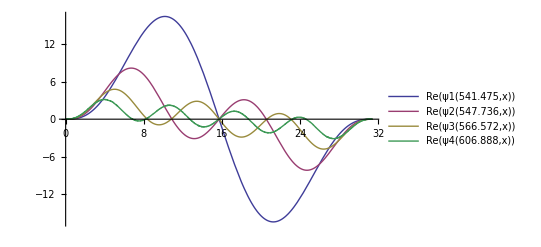

```mathematica
Plot[{Re[ψ1[ω1,x]],Re[ψ2[ω2,x]],Re[ψ3[ω3,x]],Re[ψ4[ω4,x]]},{x,0,l},PlotLegends->"Expressions",PlotRange->All,AxesOrigin->{0,0}]
```

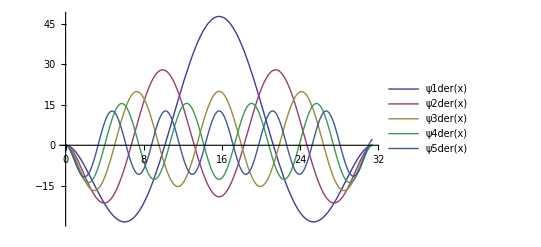

```mathematica
Plot[{ψ1der[x],ψ2der[x],ψ3der[x],ψ4der[x],ψ5der[x]},{x,0,l},PlotLegends->"Expressions",PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
(*Plot[{ψ1der2[x],ψ2der2[x],ψ3der2[x],ψ4der2[x],ψ5der2[x]},{x,0,l},PlotLegends->"Expressions",PlotRange->All,AxesOrigin->{0,0}]*)
```

```mathematica
(*Plot[{Sqrt[Re[ψ42[ω4,x]]^2+Re[ψ4der2[x]]^2]},{x,0,l},PlotLegends->"Expressions",PlotRange->All,AxesOrigin->{0,0}];*)
```

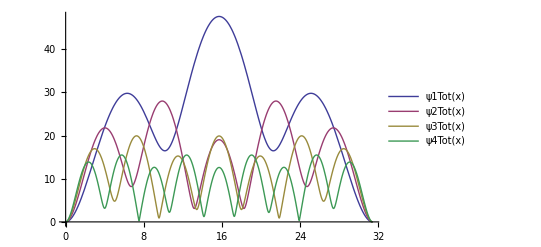

```mathematica
Plot[{ψ1Tot[x],ψ2Tot[x],ψ3Tot[x],ψ4Tot[x]},{x,0,l},PlotLegends->"Expressions",PlotRange->All,AxesOrigin->{0,0}]
```

#### Grafici parametrici

```mathematica
g0=ParametricPlot[{RCos[x/R],RSin[x/R]},{x,0,l},PlotRange->All,AspectRatio->Automatic,PlotStyle->{Black,Thick}];
```

```mathematica
gv1=ParametricPlot[{(R-0.05(ψ1der[x]))Cos[x/R],(R-0.05 (ψ1der[x]))Sin[x/R]},{x,0,l},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv2=ParametricPlot[{(R-0.05(-ψ2der[x]))Cos[x/R],(R-0.05 (-ψ2der[x]))Sin[x/R]},{x,0,l},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv3=ParametricPlot[{(R-0.05(-ψ3der[x]))Cos[x/R],(R-0.05 (-ψ3der[x]))Sin[x/R]},{x,0,l},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv4=ParametricPlot[{(R-0.05(ψ4der[x]))Cos[x/R],(R-0.05 (ψ4der[x]))Sin[x/R]},{x,0,l},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv5=ParametricPlot[{(R-0.05(-ψ5der[x]))Cos[x/R],(R-0.05 (-ψ5der[x]))Sin[x/R]},{x,0,l},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv6=ParametricPlot[{(R-0.05(ψ6der[x]))Cos[x/R],(R-0.05 (ψ6der[x]))Sin[x/R]},{x,0,27},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv7=ParametricPlot[{(R-0.05(-ψ7der[x]))Cos[x/R],(R-0.05 (-ψ7der[x]))Sin[x/R]},{x,0,20},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv8=ParametricPlot[{(R-0.05(ψ8der[x]))Cos[x/R],(R-0.05 (ψ8der[x]))Sin[x/R]},{x,0,22},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv9=ParametricPlot[{(R-0.05(ψ9der[x]))Cos[x/R],(R-0.05 (ψ9der[x]))Sin[x/R]},{x,0,R Pi/2},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

```mathematica
gv10=ParametricPlot[{(R-0.05(ψ10der[x]))Cos[x/R],(R-0.05 (ψ10der[x]))Sin[x/R]},{x,0,R Pi/2},AspectRatio->1,PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Black,Thick}];
```

## Plot parametrico delle autofunzioni

```mathematica
f1
```

86.1784

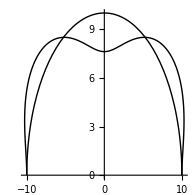

```mathematica
Show[g0,gv1]
```

```mathematica
f2
```

87.175

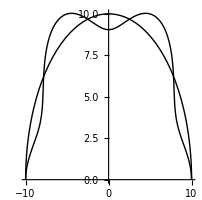

```mathematica
Show[g0,gv2]
```

```mathematica
f3
```

90.1727

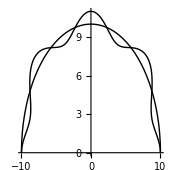

```mathematica
Show[g0,gv3]
```

```mathematica
f4
```

96.5893

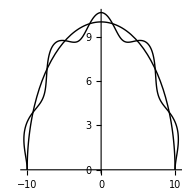

```mathematica
Show[g0,gv4]
```

```mathematica
f5
```

107.69

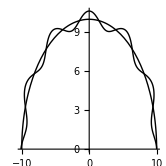

```mathematica
Show[g0,gv5]
```

```mathematica
f6
```

124.223

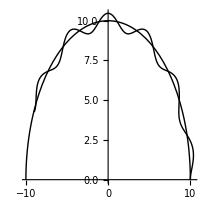

```mathematica
Show[g0,gv6]
```

```mathematica
f7
```

146.37

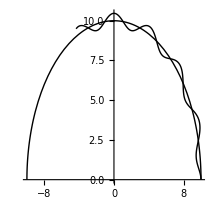

```mathematica
Show[g0,gv7]
```

```mathematica
f8
```

173.96

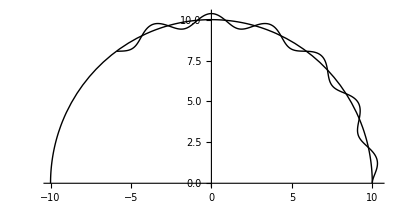

```mathematica
Show[g0,gv8]
```

```mathematica
f9
```

206.705

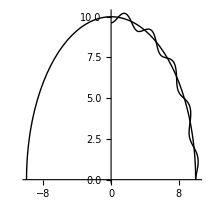

```mathematica
Show[g0,gv9]
```

```mathematica
f10
```

244.324

```mathematica
Show[g0,gv10]
```

-Graphics-

## Confronto con modello FEM: Modi Assialsimmetrici

#### Caso Analitico

```mathematica
Analitico=ListPlot[{{1,f1},{2,f2},{3,f3},{4,f4},{5,f5},{6,f6},{7,f7},{8,f8},{9,f9}},PlotStyle->{Red,PointSize[Large]},AxesLabel->{"x","y"},PlotLabel->"Grafico con punti"];
```

#### Caso Elementi finiti

```mathematica
Elemfiniti=ListPlot[{{1,64.806},{2,79.571},{3,85.767},{4,94.286},{5,107.24},{6,124.45},{7,152.47},{8,180.44},{9,213.35}},PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"x","y"},PlotLabel->"Grafico con punti"];
```

#### Confronto

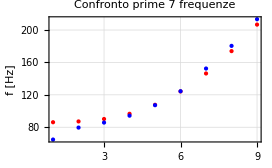

```mathematica
Show[Analitico,Elemfiniti,PlotRange->All,AxesOrigin->{0,0}, PlotLabel->"Confronto prime 7 frequenze",GridLines->Automatic,Frame->True,FrameLabel->{"x","f [Hz]"}]
```

## Confronto con modello FEM: Modi NON Assialsimmetrici

#### Caso Analitico con modi Non assialsimmetrici

```mathematica
Analitico2=ListPlot[{{1,f11},{2,f1},{3,f22},{4,f2},{5,f33},{6,f3},{7,f44},{8,f4},{9,f55},{10,f5},{11,f66},{12,f6},{13,f77},{14,f7},{15,f88},{16,f8},{17,f99},{18,f9}},PlotStyle->{Red,PointSize[Large]},AxesLabel->{"x","y"},PlotLabel->"Grafico con punti"];
```

#### Caso Elementi finiti con modi Non assialsimmetrici

```mathematica
Elemfiniti2=ListPlot[{{2,64.806},{4,79.571},{6,85.767},{8,94.286},{10,107.24},{12,124.45},{14,152.47},{16,180.44},{18,213.35}},PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"x","y"},PlotLabel->"Grafico con punti"];
```

```mathematica
Elemfiniti3=ListPlot[{{1,48.271},{3,75.6},{5,82.747},{7,89.681},{9,100.37},{11,115.98},{13,136.65 (*147.63*)},{15,165.28},{17,197.93}},PlotStyle->{Green,PointSize[Large]},AxesLabel->{"x","y"},PlotLabel->"Grafico con punti"];
```

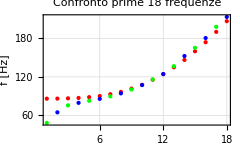

```mathematica
Show[Analitico2,Elemfiniti2,Elemfiniti3,PlotRange->All,AxesOrigin->{0,0}, PlotLabel->"Confronto prime 18 frequenze",GridLines->Automatic,Frame->True,FrameLabel->{"Frequenza i-esima","f [Hz]"}]
```

```mathematica
(*Modi FEM Assial-Simmetrici: 3, 8, 21, 36, 56, 79, 123, 152, 187*)
```

```mathematica
(*Modi FEM NON Assial-Simmetrici: 4,15,29,46,70,(96,108),134,178*)
```